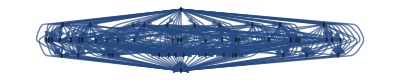

```mathematica
With[
{mat=ConversionMatrix["E","C"]},
Graph[Select[Flatten[Table[Table[If[mat[[i,j]]==1&&i≠j,i->j,123],{i,1,52}],{j,1,52}]],#=!=123&],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["G","C"]-IdentityMatrix[52],GraphLayout->"LayeredDigraphEmbedding"]}
,Table[VertexOutDegree[g,v],{v,VertexList[g]}]]//Tally//Sort
```

{{0,1},{1,10},{3,15},{4,10},{9,10},{14,5},{51,1}}

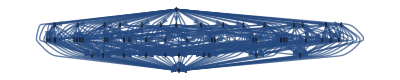
-Graphics-{52,306}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["G","C"]-IdentityMatrix[52],GraphLayout->"LayeredDigraphEmbedding"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

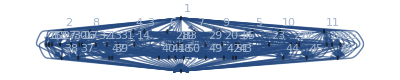
-Graphics-{52,306}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["E","C"]-IdentityMatrix[52],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

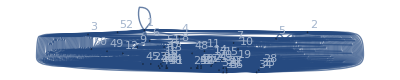
-Graphics-{52,577}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["F","C"],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["F","C"],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]}
,CompleteGraphQ[g]]
```

False

```mathematica
With[{items=Bases["F","AtomKeys"]},Table[Labeled[ShowGraph5Least[items[[k]]],k],{k,{1}}]]
```

{-Graphics-0341}

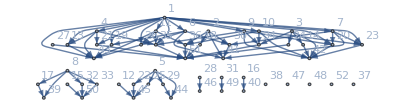
-Graphics-{52,79}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["T","C"]-IdentityMatrix[52],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

```mathematica
With[{items=Bases["T","AtomKeys"]},Table[Labeled[ShowGraph5Least[items[[k]]],k],{k,{1,4,11,6,9,10,3,7}}]]
```

{-Graphics-1993651,-Graphics-1996924,-Graphics-21420311,-Graphics-2228716,-Graphics-3313019,-Graphics-24384210,-Graphics-2002933,-Graphics-2072127}

```mathematica
With[{items=Bases["T","AtomKeys"]},Table[Labeled[ShowGraph5Least[items[[k]]],k],{k,{27,2,3,5}}]]
```

{-Graphics-20060227,-Graphics-1994032,-Graphics-2002933,-Graphics-2682135}

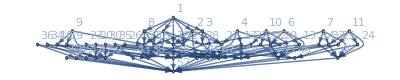
-Graphics-{52,112}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["TC","C"]-IdentityMatrix[52],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

```mathematica
With[{items=Bases["TC","AtomKeys"]},Table[Labeled[ShowGraph5Least[items[[k]]],k],{k,{1,9,4,10,6,7,11}}]]
```

{-Graphics-958831,-Graphics-1607729,-Graphics-956424,-Graphics-11701110,-Graphics-748026,-Graphics-888427,-Graphics-10291411}

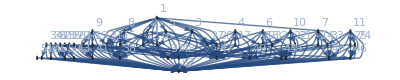
-Graphics-{52,175}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix["E","T"]-IdentityMatrix[52],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```